## (*symmetric angular parametrisation*)

```mathematica
f=3^(1/4)*M*Sqrt[2*Sin[2*x]]*Sin[x]^2/Sin[3x]
```

√2 3^(1/4) M Csc[3 x] Sin[x]^2 √Sin[2 x]

```mathematica
Series[f,{x,π/6,1}]
```

(√3 M)/4+7/4 M (x-π/6)+O[x-π/6]^2

```mathematica
l[x]=(12)^(3/4)*Sin[x]*Sqrt[Sin[2*x]]/Cos[3*x]
```

2 √2 3^(3/4) Sec[3 x] Sin[x] √Sin[2 x]

```mathematica
phi=InverseFunction[v][2/l[x]^2]
```

v^(-1)[(Cos[3 x]^2 Csc[x]^2 Csc[2 x])/(12 √3)]

```mathematica
FullSimplify[f*D[phi,x]^2,{0<x<π/6}]
```

(M (1+2 Cos[2 x]) (Cos[x]-4 Cos[3 x]+Cos[5 x])^2 Csc[x]^5)/(288 √2 3^(3/4) Sin[2 x]^(3/2) v'[v^(-1)[(Cos[3 x]^2 Csc[x]^2 Csc[2 x])/(12 √3)]]^2)

```mathematica
Series[FullSimplify[f*D[phi,x]^2,{0<x<π/6}],{x,π/6,2}]
```

(4 √3 M (x-π/6)^2)/(v'[v^(-1)[0]]^2)+O[x-π/6]^3

```mathematica
dvda =(1+2*Sin[x]^2)*Sin[6*x]/(24*Sqrt[3]*M*Sin[x]^4 * Sin[2x])
```

(Csc[x]^4 Csc[2 x] (1+2 Sin[x]^2) Sin[6 x])/(24 √3 M)

```mathematica
Series[dvda,{x,π/6,2}]
```

-(4 (x-π/6))/M+(16 √3 (x-π/6)^2)/M+O[x-π/6]^3

```mathematica
Series[1/Sin[x]^p,{x,0,2}]
```

x^-p (1+(p x^2)/6+O[x]^3)

```mathematica
ϕ=(2/λ 12^(-3/2)*Cos[3*x]^2/(Sin[x]^2*Sin[2*x])*1/M^2 )^(1/ν)
```

3^(-3/2/ν) 4^(-1/ν) ((Cos[3 x]^2 Csc[x]^2 Csc[2 x])/(M^2 λ))^(1/ν)

```mathematica
Series[Simplify[D[ϕ,x]]/.{x->α},{α,π/6,1}]
```

((-π/6+α)^2/(M^2 λ))^(1/ν) (2^(1+1/ν)/(ν (α-π/6))-(2^(3+1/ν) (2+ν))/(√3 ν^2)+(2^(1+1/ν) (1+ν) (32+11 ν) (α-π/6))/(3 ν^3)+O[α-π/6]^2)

```mathematica
l[x]=(12)^(3/4)*Sin[x]*Sqrt[Sin[2*x]]/Cos[3*x]
```

2 √2 3^(3/4) Sec[3 x] Sin[x] √Sin[2 x]

```mathematica
π
```

```mathematica
ν=4
v[g_]=g^ν;
vinv[g_]=-InverseFunction[v][g]
ϕ=Simplify[vinv[2/l[x]^2]];
dphi=Simplify[D[ϕ,x]^2]/.{x->y}
da=Simplify[Sin[3*y]/(3^(1/4) Sqrt[2 *Sin[2*y]]*Sin[y]^2 *dphi  )]
```

4

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

g^(1/4)

((-1-3 Cos[2 y]+Cos[4 y])^2 Csc[y]^5 Sec[y])/(64 3^(3/4) √(Cos[3 y]^2 Csc[y]^2 Csc[2 y]))

(32 √6 Cos[y] √(Cos[3 y]^2 Csc[y]^2 Csc[2 y]) Sin[y]^3 Sin[3 y])/((-1-3 Cos[2 y]+Cos[4 y])^2 √Sin[2 y])

```mathematica
Simplify[Series[(18 2^(5/6) 3^(3/4) Cos[y] (Cos[3 y]^2 Csc[y]^2 Csc[2 y])^(1/3) Sin[y]^3 Sin[3 y])/((-1-3 Cos[2 y]+Cos[4 y])^2 √Sin[2 y]),{y,π/6,2}],y<π/6]
```

-(3 ((-1)^(1/3) √3) (y-π/6)^(2/3))/2^(2/3)-(19 (-1)^(1/3) (y-π/6)^(5/3))/2^(2/3)+O[y-π/6]^(7/3)

```mathematica
(18 2^(5/6) 3^(3/4) Cos[y] (Cos[3 y]^2 Csc[y]^2 Csc[2 y])^(1/3) Sin[y]^3 Sin[3 y])/((-1-3 Cos[2 y]+Cos[4 y])^2 √Sin[2 y])/.{y->π/6}
```

0

```mathematica
Simplify[Series[dphi,{y,π/6,1}],y<π/6]
```

(4 (-2)^(2/3))/(9 (y-π/6)^(2/3))-(160 (-2)^(2/3) (y-π/6)^(1/3))/(27 √3)+O[y-π/6]^(4/3)

```mathematica
dphi/.{y[x]->π/6}
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
Simplify[Sin[3*y]/(3^(1/4) Sqrt[2 *Sin[2*y]]*Sin[y]^2 *dphi  )]
```

(18 2^(5/6) 3^(3/4) Cos[y] (Cos[3 y]^2 Csc[y]^2 Csc[2 y])^(1/3) Sin[y]^3 Sin[3 y])/((-1-3 Cos[2 y]+Cos[4 y])^2 √Sin[2 y])

```mathematica
NIntegrate[Simplify[1/(Sin[3*y]/(3^(1/4) Sqrt[2 *Sin[2*y]]*Sin[y]^2 *dphi ) )],{y,0.1,π/6}]
```

2.22859

```mathematica
Simplify[Series[Simplify[1/(Sin[3*y]/(3^(1/4) Sqrt[2 *Sin[2*y]]*Sin[y]^2 *dphi ) )],{y,π/6,1}],y<π/6]
```

-(√(3/2))/(8 (y-π/6))+5/(8 √2)-(43 (y-π/6))/(16 √6)+O[y-π/6]^2

```mathematica
NIntegrate[-(√(3/2))/(8 (y-π/6)),{y,0.1,π/6-0.01}]
```

0.573518

```mathematica
NIntegrate[1/(x-π/6),{x,0,π/6}]
```

-36.7491

10

4

20 √2 3^(3/4) Sec[3 x] Sin[x] √Sin[2 x]

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

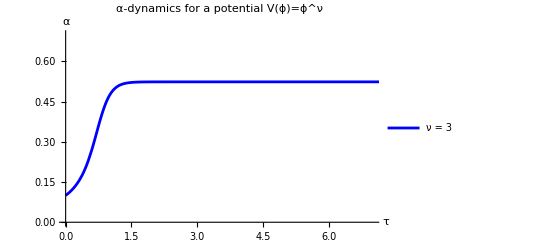

```mathematica
M =10
ν=4
l[x]=(12)^(3/4)*Sin[x]*Sqrt[Sin[2*x]]/Cos[3*x]*M
v[g_]=g^ν;
vinv[g_]=-(-1)^ν*InverseFunction[v][g];
ϕ=Simplify[vinv[2/l[x]^2]];
dphi=Simplify[D[ϕ,x]^2]/.{x->y[x]};
s=NDSolve[{y'[x]==Simplify[Sin[3*y[x]]/(M*3^(1/4) Sqrt[2 *Sin[2*y[x]]]*Sin[y[x]]^2 *dphi  )],y[0]==0.1},y,{x,0,100}];
Plot[Evaluate[y[x]/. s],{x,0,30},PlotRange->{{0,7},{0,0.7}},PlotStyle->Blue,PlotLegends->{"ν = 3"},AxesLabel->{τ,α},PlotLabel->"α-dynamics for a potential V(ϕ)=ϕ^ν"]
```

```mathematica
DSolve[y'[x]==Simplify[Sin[3*y[x]]/(M*3^(1/4) Sqrt[2 *Sin[2*y[x]]]*Sin[y[x]]^2 *dphi  )],y[x],x]
```

$Aborted

```mathematica
y[x]/. s[[1]]
```

InterpolatingFunction[…][x]

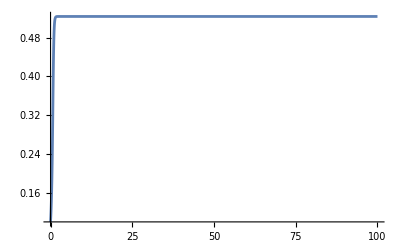

```mathematica
Plot[%151,{x,0.,100},PlotRange->Full]
```

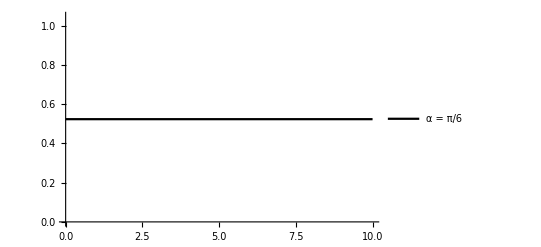

```mathematica
p0=Plot[x*0+π/6,{x,0,10},PlotStyle->{Thick,Black},PlotLegends->{"α = π/6"}]
```

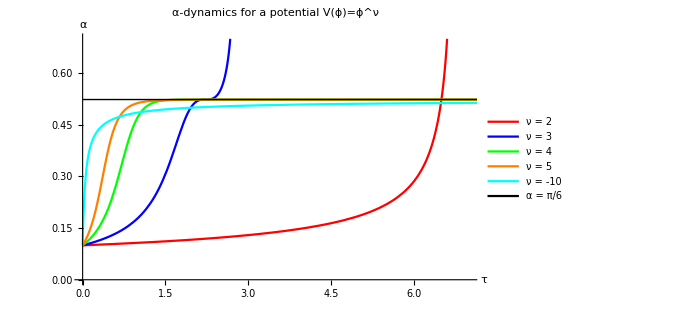

```mathematica
Show[p1,p2,p3,p4,p5,p0]
```

```mathematica
v[g_]=g^ν
```

g^3

```mathematica
vinv=.
```

```mathematica
vinv[g_]=-(-1)^ν*InverseFunction[v][g]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

g^(1/3)

```mathematica
ϕ=.
```

```mathematica
ϕ=Simplify[vinv[2/l[x]^2]]
```

((Cos[3 x]^2 Csc[x]^2 Csc[2 x])^(1/3))/(2^(2/3) √3)

```mathematica
dphi=Simplify[D[ϕ,x]^2]/.{x->y[x]}
```

((-1-3 Cos[2 y[x]]+Cos[4 y[x]])^2 Csc[y[x]]^5 Sec[y[x]])/(108 2^(1/3) (Cos[3 y[x]]^2 Csc[y[x]]^2 Csc[2 y[x]])^(1/3))

```mathematica
Simplify[D[ϕ,x]^2]/.{x->π/6}
```

Power::infy: Infinite expression 1/0^(1/3) encountered.

ComplexInfinity

```mathematica
N[π/6]
```

0.523599

```mathematica
Simplify[Sin[3*y[x]]/(3^(1/4) Sqrt[2 *Sin[2*y[x]]]*Sin[y[x]]^2 *dphi  )]
```

(32 √6 Cos[y[x]] √(Cos[3 y[x]]^2 Csc[y[x]]^2 Csc[2 y[x]]) Sin[y[x]]^3 Sin[3 y[x]])/((-1-3 Cos[2 y[x]]+Cos[4 y[x]])^2 √Sin[2 y[x]])

```mathematica
(-1-3 Cos[2 y[x]]+Cos[4 y[x]])^2/.{y[x]->π/6}
```

9

4

2 √2 3^(3/4) Sec[3 x] Sin[x] √Sin[2 x]

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

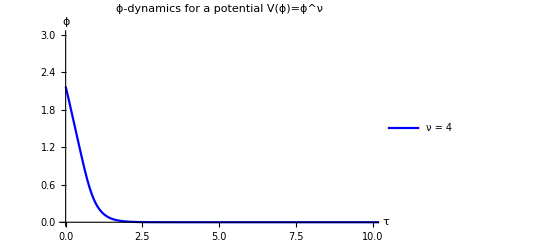

```mathematica
ν=4
l[x]=(12)^(3/4)*Sin[x]*Sqrt[Sin[2*x]]/Cos[3*x]
v[g_]=g^ν;
vinv[g_]=-(-1)^ν*InverseFunction[v][g];
ϕ=Simplify[vinv[2/l[x]^2]];
dphi=Simplify[D[ϕ,x]^2]/.{x->y[x]};
s=NDSolve[{y'[x]==Simplify[Sin[3*y[x]]/(3^(1/4) Sqrt[2 *Sin[2*y[x]]]*Sin[y[x]]^2 *dphi  )],y[0]==0.1},y,{x,0,100}];
Plot[Evaluate[ϕ/.{x->(y[x]/. s)}],{x,0,30},PlotRange->{{0,10},{0,3}},PlotStyle->Blue,PlotLegends->{"ν = 4"},AxesLabel->{τ,"ϕ"},PlotLabel->"ϕ-dynamics for a potential V(ϕ)=ϕ^ν"]
```

```mathematica
Solve[(12)^(3/4)*Sin[x]*Sqrt[Sin[2*x]]/Cos[3*x]*M==1 &&2^(3/2)/3^(1/4)*M*Sin[x]*Sqrt[Sin[2*x]]==1,{x,M}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
α1=y/.First@s
```

InterpolatingFunction[…]

```mathematica
α1'[0]
```

0.121185

```mathematica
m=.
```

```mathematica
m[τ_]=2^(3/2)/3^(1/4)*M*Sin[α1[τ]]*Sqrt[Sin[2*α1[τ]]]*M
```

(200 √2 Sin[InterpolatingFunction[…][τ]] √Sin[2 InterpolatingFunction[…][τ]])/3^(1/4)

```mathematica
l[τ_]=(12)^(3/4)*Sin[α1[τ]]*Sqrt[Sin[2*α1[τ]]]/Cos[3*α1[τ]]*M
```

20 √2 3^(3/4) Sec[3 InterpolatingFunction[…][τ]] Sin[InterpolatingFunction[…][τ]] √Sin[2 InterpolatingFunction[…][τ]]

```mathematica
m[1]
```

88.1661

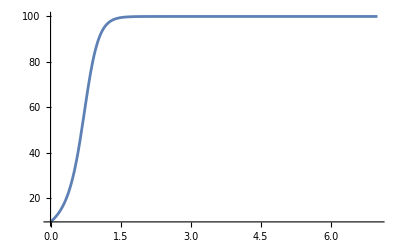

```mathematica
Plot[m[x],{x,0,7},PlotRange->Full]
```

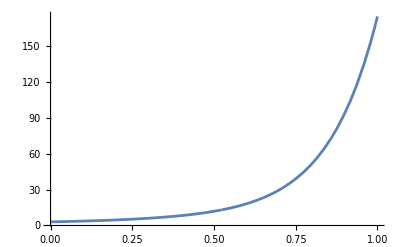

```mathematica
Plot[l[x],{x,0,1},PlotRange->Full]
```

```mathematica
β[τ_]=16*M^2*Sin[α1[τ]]^2
```

1600 Sin[InterpolatingFunction[…][τ]]^2

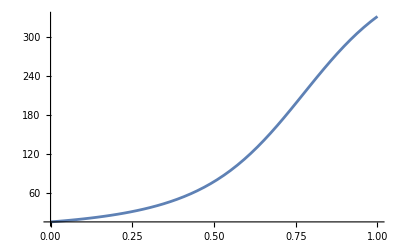

```mathematica
Plot[β[x],{x,0,1},PlotRange->Full]
```

```mathematica
γ[τ_]=(1+2*Sin[α1[τ]]^2)*Cos[3*α1[τ]]/(108^(3/4)*M*Sin[α1[τ]]^2*Sqrt[Sin[2*α1[τ]]])
```

(Cos[3 InterpolatingFunction[…][τ]] Csc[InterpolatingFunction[…][τ]]^2 (1+2 Sin[InterpolatingFunction[…][τ]]^2))/(180 √2 3^(1/4) √Sin[2 InterpolatingFunction[…][τ]])

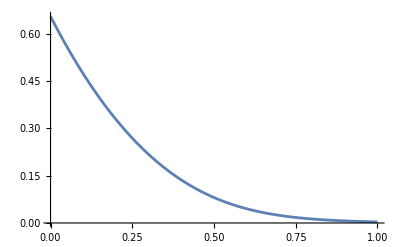

```mathematica
Plot[γ[x],{x,0,1},PlotRange->Full]
```

## check γ and β between paper and dropbox

```mathematica
f=(12)^(3/4)*Sin[x]*Sqrt[Sin[2*x]]/Cos[3*x]*mm
```

2 √2 3^(3/4) mm Sec[3 x] Sin[x] √Sin[2 x]

```mathematica
f^2/(3*Sqrt[3])*(1-2*Cos[2*x])^2*Cot[x]
```

8 mm^2 Cos[x] (1-2 Cos[2 x])^2 Sec[3 x]^2 Sin[x] Sin[2 x]

```mathematica
Simplify[8 mm^2 Cos[x] (1-2 Cos[2 x])^2 Sec[3 x]^2 Sin[x] Sin[2 x]]
```

16 mm^2 Sin[x]^2

```mathematica
(2-Cos[2*x])/Sin[x]*1/(3*Sqrt[3]*f)
```

((2-Cos[2 x]) Cos[3 x] Csc[x]^2)/(18 √2 3^(1/4) mm √Sin[2 x])

```mathematica
Simplify[((2-Cos[2 x]) Cos[3 x] Csc[x]^2)/(18 √2 3^(1/4) mm √Sin[2 x])-(1+2*Sin[x]^2)*Cos[3*x]/(108^(3/4)*mm*Sin[x]^2*Sqrt[Sin[2*x]])]
```

0